9

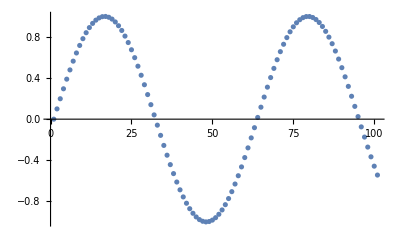

```mathematica
(*Ensure frequency extraction is accurate*)
DataLength=10.;
SamplingRate=0.1;
XVals=Range[0,DataLength,SamplingRate];

data=Sin[5.12*XVals];
PowerSpec=(Abs[Fourier[data]]^2)[[1;;Round[DataLength/(SamplingRate*2)]]];
PowerPeaks=FindPeaks[PowerSpec];

PeakIndex=TakeLargestBy[PowerPeaks,Last,1]⟦1,1⟧

ListPlot[origFunc]
```